## Data Import

Set this to wherever this file is.

```mathematica
SetDirectory["~/Thesis/Calculations/"]
```

/home/ellen/Thesis/Calculations

These files contain the data from the numerical runs.

```mathematica
l0=Import["l0.csv"];
l1=Import["l1.csv"];
l2=Import["l2.csv"];
l3=Import["l3.csv"];
l4=Import["l4.csv"];
l5=Import["l5.csv"];
l6=Import["l6.csv"];
l7=Import["l7.csv"];
l8=Import["l8.csv"];
l9=Import["l9.csv"];
l10=Import["l10.csv"];
```

```mathematica
ls={l0,l1,l2,l3,l4,l5,l6,l7,l8,l9,l10};
```

```mathematica
lsplot=Table[Table[{j,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}];
```

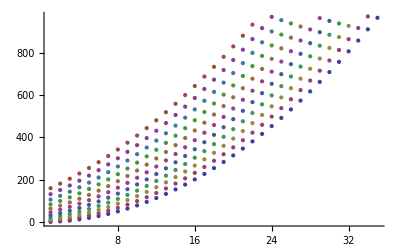

```mathematica
ListPlot[lsplot]
```

List plot with fits!

```mathematica
Show[ListPlot[lsplot,PlotRange->{0,1000},AxesLabel->{"n","λ_n"}],Plot[Table[(a + b x + c x^2)/.Fits[[i]],{i,1,Length[Fits]}],{x,0,35}]]
```

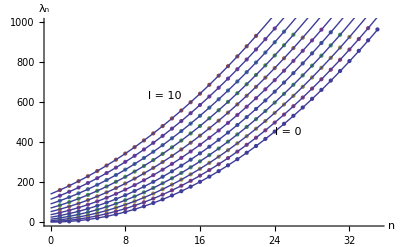

```mathematica
lsplot2=Table[Table[{j+i-1,ls[[i,j,1]]},{j,1,Length[ls[[i]]]}],{i,1,Length[ls]}];
```

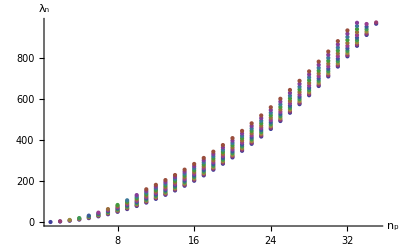

```mathematica
ListPlot[lsplot2,AxesLabel->{"n_p","λ_n"}]
```

## Least Squares Fit

### Weighted linear least-squares fit (ultimately unsuccessful)

```mathematica
loglog=Table[{Log[N[i]],Log[l0[[i,1]]],1/l0[[i,1]]*l0[[i,2]]},{i,1,Length[l0]}];
```

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

These are the fit coefficients (for line of form y = A + Bx):

```mathematica
A=1/Delta (Sum[w[i]*x[i]^2,{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}])
```

-0.224553

```mathematica
B=1/Delta (Sum[w[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}])
```

1.99448

This came out not quite quadratic. We can plot the fit on the data:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

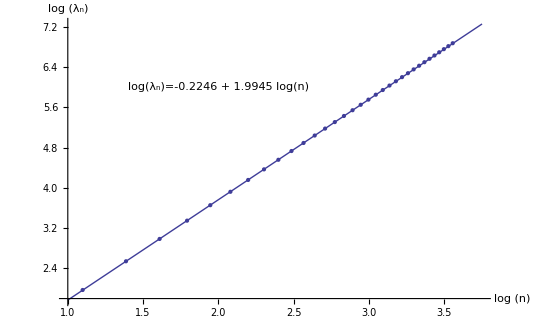

```mathematica
Show[Plot[F[x],{x,1.,3.75},AxesLabel->{"log (n)","log (\!\(\*SubscriptBox[\(λ\), \(n\)]\))"}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,Length[loglog]}]],Graphics[Text[Style["log(\!\(\*SubscriptBox[\(λ\), \(n\)]\))=-0.2246 + 1.9945 log(\!\(\*
StyleBox[\"n\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\")\",\nFontSlant->\"Italic\"]\)",Medium],{2.0,6}]]]
```

Now we can check the goodness of fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

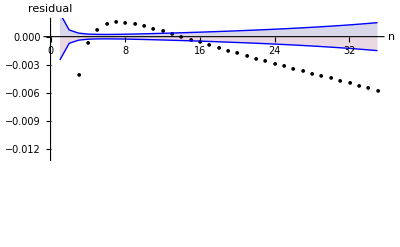

```mathematica
Show[ListPlot[residuals,PlotStyle->Black,PlotMarkers->{Automatic,5},AxesLabel->{"n","residual"}],ListPlot[{Table[loglog[[i,3]],{i,1,Length[loglog]}],Table[-loglog[[i,3]],{i,1,Length[loglog]}]},PlotStyle->Blue,Joined->True,Filling->Axis]]
```

This fit sucks.

### Polynomial least-squares fit functions

Implementation of a polynomial least squares fit.

```mathematica
PolyFit[lambdas_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Inverse[M].{Sum[lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]*lambdas[[i,2]],{i,1,Length[lambdas]}],
Sum[lambdas[[i,1]]^2*lambdas[[i,2]],{i,1,Length[lambdas]}]};
Return[{a->res[[1]],b->res[[2]],c->res[[3]]}]
]
```

```mathematica
WeightedPolyFit[lambdas_]:=Module[{M,len,res},
len=Length[lambdas];
M=({{Sum[1/lambdas[[i,2]]^2,{i,1,len}], Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}], Sum[i^4/lambdas[[i,2]]^2,{i,1,len}]}});
res=Inverse[M].{Sum[lambdas[[i,1]]/lambdas[[i,2]]^2,{i,1,len}],
Sum[i*lambdas[[i,1]]/lambdas[[i,2]]^2,{i,1,len}],
Sum[i^2*lambdas[[i,1]]/lambdas[[i,2]]^2,{i,1,len}]};
Return[{a->res[[1]],b->res[[2]],c->res[[3]]}]
]
```

```mathematica
DeltaYs[lambdas_,fit_]:=Sqrt[1/(Length[lambdas]-3)Sum[(lambdas[[i,2]]-(a+b lambdas[[i,1]]+c lambdas[[i,1]]^2)/.fit)^2,{i,1,Length[lambdas]}]]
```

```mathematica
DeltaABCs[lambdas_,fit_,dy_]:=Module[{M,res},
M=({{Length[lambdas], Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]],{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}]}, {Sum[lambdas[[i,1]]^2,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^3,{i,1,Length[lambdas]}], Sum[lambdas[[i,1]]^4,{i,1,Length[lambdas]}]}});
res=Sqrt[Sum[(Inverse[M].{1,
lambdas[[i,1]],
lambdas[[i,1]]^2}*dy)^2,{i,1,Length[lambdas]}]];
Return[res]
]
```

```mathematica
WeightedDeltaABCs[lambdas_]:=Module[{M,len,res},
len=Length[lambdas];
M=({{Sum[1/lambdas[[i,2]]^2,{i,1,len}], Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i/lambdas[[i,2]]^2,{i,1,len}], Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}]}, {Sum[i^2/lambdas[[i,2]]^2,{i,1,len}], Sum[i^3/lambdas[[i,2]]^2,{i,1,len}], Sum[i^4/lambdas[[i,2]]^2,{i,1,len}]}});
res=Table[Sqrt[Inverse[M][[i,i]]],{i,1,3}];
Return[res]
]
```

### Polynomial fits and analysis

```mathematica
Fits=Table[PolyFit[lsplot[[i]]],{i,2,Length[lsplot]}];
```

```mathematica
ftest=WeightedPolyFit[l0];
```

Different data collection methods meant using different fit types for the l = 0 data and the rest.

```mathematica
Fits=Join[{ftest},Fits];
```

```mathematica
dys=Table[DeltaYs[lsplot[[i]],Fits[[i]]],{i,2,Length[Fits]}];
```

```mathematica
dys=Join[{{}},dys];
```

```mathematica
TableForm[Table[Join[{"l = "<>ToString[i-1]},Fits[[i]],{dys[[i]]}],{i,1,Length[Fits]}]]
```

l = 0 | a→0.0437591 | b→0.0180773 | c→0.78578 | 
l = 1 | a→0.0437591 | b→0.0180773 | c→0.78578 | 
l = 2 | a→2.08389 | b→1.87181 | c→0.783359 | 0.061561
l = 3 | a→6.69914 | b→3.7623 | c→0.780989 | 0.0999442
l = 4 | a→13.9713 | b→5.66987 | c→0.778668 | 0.126059
l = 5 | a→23.916 | b→7.58959 | c→0.776349 | 0.141452
l = 6 | a→36.5484 | b→9.5174 | c→0.774072 | 0.148596
l = 7 | a→51.8423 | b→11.4602 | c→0.77144 | 0.140831
l = 8 | a→69.8763 | b→13.3975 | c→0.769258 | 0.136714
l = 9 | a→90.6213 | b→15.3367 | c→0.767164 | 0.129699
l = 10 | a→114.081 | b→17.2771 | c→0.765162 | 0.12079
l = 11 | a→140.221 | b→19.2291 | c→0.762649 | 0.101198

Goodness of fit for l = 0:

```mathematica
G[x_]:=c x^2+b x+a/.Fits[[1]]
```

```mathematica
quadfitvals=Table[G[i],{i,1,Length[l0]}];
```

```mathematica
quadresiduals=Table[quadfitvals[[i]]-l0[[i,1]],{i,1,Length[l0]}];
```

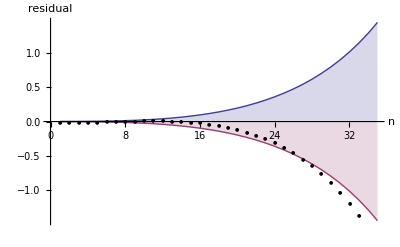

```mathematica
Show[ListPlot[{Table[l0[[i,2]],{i,1,Length[l0]}],Table[-l0[[i,2]],{i,1,Length[l0]}]},Joined->True,Filling->Axis,AxesLabel->{"n","residual"}],ListPlot[quadresiduals,PlotStyle->Black,PlotMarkers->{Automatic,5}]]
```

This fit is much better! Additional info:

```mathematica
dabcs=Table[DeltaABCs[lsplot[[i]],Fits[[i]],dys[[i]]],{i,2,Length[lsplot]}]
```

{{0.0336319,0.00443055,0.000122796},{0.0564978,0.0078931,0.00023205},{0.0725534,0.0104523,0.000316912},{0.0829445,0.0123341,0.000386055},{0.0888369,0.0136497,0.000441511},{0.0877272,0.01444,0.000500517},{0.0870456,0.0148573,0.000534104},{0.0844883,0.0149742,0.000559067},{0.0805912,0.0148535,0.000576805},{0.0710914,0.0142391,0.000601176}}

```mathematica
dabcs=Join[{WeightedDeltaABCs[l0]},dabcs]
```

{{0.0028406,0.00145906,0.000149063},{0.0336319,0.00443055,0.000122796},{0.0564978,0.0078931,0.00023205},{0.0725534,0.0104523,0.000316912},{0.0829445,0.0123341,0.000386055},{0.0888369,0.0136497,0.000441511},{0.0877272,0.01444,0.000500517},{0.0870456,0.0148573,0.000534104},{0.0844883,0.0149742,0.000559067},{0.0805912,0.0148535,0.000576805},{0.0710914,0.0142391,0.000601176}}

```mathematica
dabcs//TableForm
```

0.0028406 | 0.00145906 | 0.000149063
0.0336319 | 0.00443055 | 0.000122796
0.0564978 | 0.0078931 | 0.00023205
0.0725534 | 0.0104523 | 0.000316912
0.0829445 | 0.0123341 | 0.000386055
0.0888369 | 0.0136497 | 0.000441511
0.0877272 | 0.01444 | 0.000500517
0.0870456 | 0.0148573 | 0.000534104
0.0844883 | 0.0149742 | 0.000559067
0.0805912 | 0.0148535 | 0.000576805
0.0710914 | 0.0142391 | 0.000601176

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
as=Table[{i-1,a/.Fits[[i,1]]},{i,1,Length[Fits]}]
```

{{0,0.0437591},{1,2.08389},{2,6.69914},{3,13.9713},{4,23.916},{5,36.5484},{6,51.8423},{7,69.8763},{8,90.6213},{9,114.081},{10,140.221}}

```mathematica
aserr=Table[{{i-1,a/.Fits[[i,1]]},ErrorBar[dabcs[[i,1]]]},{i,1,Length[Fits]}];
```

```mathematica
bs=Table[{i-1,b/.Fits[[i,2]]},{i,1,Length[Fits]}]
```

{{0,0.0180773},{1,1.87181},{2,3.7623},{3,5.66987},{4,7.58959},{5,9.5174},{6,11.4602},{7,13.3975},{8,15.3367},{9,17.2771},{10,19.2291}}

```mathematica
bserr=Table[{{i-1,b/.Fits[[i,2]]},ErrorBar[dabcs[[i,2]]]},{i,1,Length[Fits]}];
```

```mathematica
cs=Table[{i-1,c/.Fits[[i,3]]},{i,1,Length[Fits]}]
```

{{0,0.78578},{1,0.783359},{2,0.780989},{3,0.778668},{4,0.776349},{5,0.774072},{6,0.77144},{7,0.769258},{8,0.767164},{9,0.765162},{10,0.762649}}

```mathematica
cserr=Table[{{i-1,c/.Fits[[i,3]]},ErrorBar[dabcs[[i,3]]]},{i,1,Length[Fits]}];
```

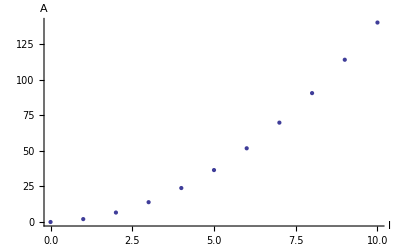

```mathematica
ErrorListPlot[aserr,AxesLabel->{"l","A"}]
```

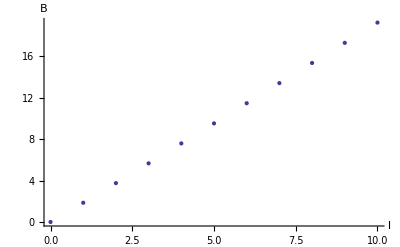

```mathematica
ErrorListPlot[bserr,AxesLabel->{"l","B"}]
```

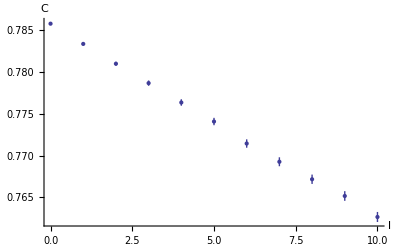

```mathematica
ErrorListPlot[cserr,AxesLabel->{"l","C"}]
```